## Subradiance-protected excitation spreading for collimated photon emission

See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

## setup

```mathematica
(*PARAMETERS and other DEFINITIONS*)
atomnum = 16;
J = 1; (*upper level total angular momentum*) 
λ = 7.8*10^-7;
k =2π/λ;
a=0.7 λ; (*atomic grid spatial period*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
deg = 2J+1;
dim = deg*atomnum; (*Hamiltonian shape is dim x dim*)
Hfull = Array[Subscript[H, ##]&,{dim,dim}];
(*FUNCTIONS*)
Subscript[r, i_,j_]=a{Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->atomnum;(*distance between atoms i,j*)
sphrWave[x_,y_,z_]=(ⅇ^(ⅈ k √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2));(*spherical wave*)
Subscript[Kδ, μ_,ν_]:=KroneckerDelta[SymbolName[μ],SymbolName[ν]];(*symbolic Kronecker delta*)
dipOp[α_,β_]=(D[#,α]D[#,β]-Subscript[Kδ, α,β] Laplacian[#,{x,y,z}]-Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])&; (*derivative op in the expression for positive freq. component of monochromatic dipole radation*)
Subscript[G, α_,β_]:=dipOp[α,β][sphrWave[x,y,z]];(*element (α,β) of the positive frequency compenent of monochromatic dip. radiation*)
GTensor = Table[Subscript[G, α,β]+(Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])/3,{α,{x,y,z}},{β,{x,y,z}}];
Subscript[e, μ_] := {1/(√2){1,0,-ⅈ 1},{1,0,0},1/(√2){1,0,+ⅈ 1}}[[μ]];(*polarization basis. μ=1,2,3 -> polarization σ=-1,0,+1 *)
Subscript[dipRadKernel, μ_,ν_,i_,j_]:=Subscript[e, μ]*.GTensor.Subscript[e, ν]/.{x-> u[[1]],y->u[[2]],z-> 0}/.u-> Subscript[r, i,j] (*element (μ,ν) of the dipole radiation kernel between atoms i,j*)
```

```mathematica
Clear[dipRadKernel,testkernel]
```

```mathematica
Subscript[dipRadKernel, μ_,ν_,i_,j_]:=Subscript[e, μ]*.GTensor.Subscript[e, ν]/.{x-> u[[1]],y->u[[2]],z-> 0}/.u-> Subscript[r, i,j] (*element (μ,ν) of the dipole radiation kernel between atoms i,j*)
```

```mathematica
Subscript[dipRadKernel, 1,1,1,2]
```

7.12943×10^23-1.30621×10^23 ⅈ

```mathematica
Subscript[dipRadKernel, 1,1]/.{x-> u[[1]],y->u[[2]],z-> 0}/.u-> {1,2}
```

```mathematica
Subscript[testkernel, μ_,ν_,i_,j_]:=Subscript[e, μ]*.GTensor.Subscript[e, ν] /.{x-> u[[1]],y->u[[2]],z-> 0}/.u-> Subscript[r, i,j]
```

```mathematica
Subscript[testkernel, 1,1,1,3]
```

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

Part::partd: Part specification u⟦2⟧ is longer than depth of object.

-8.98148×10^22+1.49643×10^23 ⅈ

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

Part::partd: Part specification u⟦2⟧ is longer than depth of object.

9.53202×10^11-2.09968×10^12 ⅈ

```mathematica
Subscript[e, 0]*.GTensor.Subscript[e, 0]
```

```mathematica
Subscript[e, 0]*
```

Conjugate[List]

```mathematica
(Subscript[e, μ]*.GTensor.Subscript[e, ν])/.{x-> u[[1]],y->u[[2]],z-> 0}/.u-> {1,2,3}
```

```mathematica
foobar[x_,y_,z_]:=x y z;
foobar[x,y,z]/.({x-> u[[1]],y->u[[2]],z-> 3}/.u-> {1,2})
```

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

Part::partd: Part specification u⟦2⟧ is longer than depth of object.

6

```mathematica
{ u[[1]],u[[2]]}/.u-> {1,2}
```

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

Part::partd: Part specification u⟦2⟧ is longer than depth of object.

{1,2}

```mathematica
{1,2}[[1]]
```

1

TODO make dipRadKernel also take atomic position subscripts.

Hamiltonian matrix elements: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), where μ,⋁ specify polarization projections and j,k are the atom indices in the 2D grid.

TODO: find what values the paper used for Ω,Δ,γ, then build those into the Hamiltonian.

TODO: define the dipole radiation kernel and then break into real and imaginary parts to get the Rabi frequency

```mathematica
(*need to evaluate each term's derivative symbolically then numerically at the coordinates for the atom pair*)
G = Table[dipRadKernel[α,β][sphrWave[ x,y,z]],{α,{x,y,z}},{β,{x,y,z}}];(*this is G[Subscript[r, ij]]'. Need Subscript[G, μν]^ij. G is in Cartesian. I express the spherical basis vectors in Cartesian space. Find a way to "dot" these vectors with the Table G*)
```

```mathematica
(*fill the Hamiltonian*)
For[j=1,j<Length[atomnum]+1,j++,
For[k=1,k<Length[atomnum]+1,k++,
For[ν=1,ν<Length[pol]+1,ν++,
For[μ=1,μ<Length[pol]+1,μ++,
Hfull[[3(j-1)+ν,3(k-1)+μ]]= Subscript[Δ, μ] KroneckerDelta[j,k]KroneckerDelta[μ,ν]+Subscript[Ω, μ,ν,j,k](1-Subscript[δ, j,k])+ⅈ Subscript[γ, μ,ν,j,k];
]
]
]
]
```

```mathematica
3*atomnum-1+deg
```

50

```mathematica
Length[pol]
```

3

```mathematica
3atomnum
```

48

```mathematica
3*(atomnum-1)+deg
```

48

```mathematica
A = Array[Subscript[a, ##]&,{2,2}]
```

{{a_(1,1),a_(1,2)},{a_(2,1),a_(2,2)}}

```mathematica
A[[1,1]]
```

a_(1,1)

evaluate a derivative in a table, then evaluate each entry numerically

```mathematica
foo[x_,y_,z_]:=x^2+y^2+z^2;
Table[D[foo[x,y,z],α],{α,{x,y,z}}]/.{x-> 1,y->1,z->1}
```

{2,2,2}

Check my grid mapping. 2D grid, but only one index to specify atoms

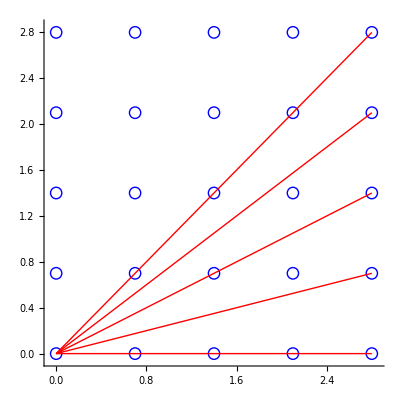

```mathematica
num=5;
a=0.7;
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
Show[Table[Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],{i,Range[num^2]}],Table[r[1,j],{j,{5,10,15,20,25}}],Axes->True]
```

```mathematica
r[i_,j_] :=a{Mod[j-1,num]-Mod[i-1,num],Floor[(j-1)/num]-Floor[(i-1)/num]};
```

```mathematica
r[1,15]
```

{2.8,1.4}

```mathematica
υ = Table[x^2+y^2,{x,{-1,0,1}},{y,{-1,0,1}}]
```

{{2,1,2},{1,0,1},{2,1,2}}

```mathematica
{1,0,1}.υ
```

{4,2,4}